```mathematica
[1,2,1],[0,0.9999*2,-0.9999]
```

```mathematica
resp=(1+2z+z^2)/(1-2z+z^2)/.z->Exp[2Pi I f]
```

(1+2 ⅇ^(2 ⅈ f π)+ⅇ^(4 ⅈ f π))/(1-2 ⅇ^(2 ⅈ f π)+ⅇ^(4 ⅈ f π))

```mathematica
Simplify[ExpToTrig[resp]]
```

-Cot[f π]^2

```mathematica
Together[Simplify[TrigToExp[Cot[Pi f]]]/.Exp[2Pi I f]->z]
```

(ⅈ (1+z))/(-1+z)

```mathematica
Together[Simplify[TrigToExp[Cot[Pi f]^2]]/.Exp[2Pi I f]->z]
```

-(1+z)^2/(-1+z)^2

```mathematica
exprq[n_]:=Simplify[PadeApproximant[(1+z)^2/(-1+z)^2,{z,0,{n,n}}]]
```

```mathematica
Join[{1},Table[Coefficient[Expand[Numerator[exprq[3]]],z^n]/(Numerator[exprq[3]]/.z->0),{n,1,2}]]
```

{1,2,1}

```mathematica
Join[{0},Table[-Coefficient[Expand[Denominator[exprq[3]]],z^n]/(Numerator[exprq[3]]/.z->0),{n,1,2}]]
```

{0,2,-1}

```mathematica
exprn[n_]:=Simplify[PadeApproximant[((1+z)/(1-z))^(3/2),{z,0,{n,n}}]]
```

```mathematica
exprn[n_,m_]:=Simplify[PadeApproximant[((1+z)/(1-z))^(3/2),{z,0,{n,m}}]]
```

```mathematica
exprns[n_]:=Normal[Series[((1+z)/(1-z))^(3/2),{z,0,n}]]
```

```mathematica
N[Solve[Denominator[exprq[2]]==0]]
```

{{z→1.},{z→1.}}

```mathematica
Denominator[exprn[32]]
```

-270582939648+405874409472 z+1830729809920 z^2-2915209052160 z^3-5488162897920 z^4+9427184779264 z^5+9563415773184 z^6-18137512673280 z^7-10648918425600 z^8+23113551052800 z^9+7787941724160 z^10-20554648125440 z^11-3621204787200 z^12+13092048076800 z^13+882088345600 z^14-6033484283904 z^15+48199827456 z^16+2008326144000 z^17-120499568640 z^18-476759162880 z^19+45027254272 z^20+78737498112 z^21-9029529600 z^22-8685547520 z^23+1064194560 z^24+599818752 z^25-71194368 z^26-23304960 z^27+2399040 z^28+418880 z^29-31008 z^30-2208 z^31+65 z^32

```mathematica
Chop[N[Solve[Denominator[exprn[32]]==0]]]
```

{{z→-13.7924},{z→-5.93413},{z→-3.80291},{z→-2.81737},{z→-2.25422},{z→-1.89344},{z→-1.64545},{z→-1.467},{z→-1.33472},{z→-1.2349},{z→-1.15903},{z→-1.10164},{z→-1.05909},{z→-1.02895},{z→-1.00964},{z→0.999319},{z→1.00372},{z→1.01801},{z→1.04258},{z→1.07869},{z→1.12829},{z→1.19437},{z→1.28137},{z→1.39611},{z→1.5493},{z→1.7587},{z→2.05574},{z→2.50161},{z→3.233},{z→4.62987},{z→8.28838},{z→41.3451}}

```mathematica
N[Solve[12-18 z+5 z^2==0,z]]
```

{{z→0.883485},{z→2.71652}}

```mathematica
Join[{1},Table[Coefficient[Expand[Numerator[exprn[2]]],z^n]/(Numerator[exprn[2]]/.z->0),{n,1,4}]]
```

{1,3/2,5/12,0,0}

```mathematica
Join[{0},Table[-Coefficient[Expand[Denominator[exprn[2]]],z^n]/(Numerator[exprn[2]]/.z->0),{n,1,4}]]
```

{0,3/2,-5/12,0,0}

```mathematica
Join[{1},Table[N[Coefficient[Expand[Numerator[exprn[32]]/(I 270582939648)],z^n],15],{n,1,32}]]
```

{1,1.5,-6.765873015873,-10.7738095238095,20.2827380952381,34.8402777777778,-35.34375,-67.03125,39.35546875,85.4213169642857,-28.7820870535714,-75.9643167162698,13.382975260417,48.3846028645833,-3.2599555121528,-22.298095703125,-0.178133283342634,7.42222013927641,0.445333208356585,-1.76197052001953,-0.166408326890734,0.290992101033529,0.0333706537882487,-0.0320993907867916,-0.00393296991075788,0.00221676485879081,0.000263114770253499,-0.0000861287117004395,-8.86619091033936×10^-6,1.54806507958306×10^-6,1.14597025371733×10^-7,-8.16015970139276×10^-9,-2.4022209265875×10^-10}

```mathematica
Join[{0},Table[-N[Coefficient[Expand[Denominator[exprn[32]]/270582939648],z^n],15],{n,1,32}]]
```

{0,-1.5,-6.765873015873,10.7738095238095,20.2827380952381,-34.8402777777778,-35.34375,67.03125,39.35546875,-85.4213169642857,-28.7820870535714,75.9643167162698,13.382975260417,-48.3846028645833,-3.2599555121528,22.298095703125,-0.178133283342634,-7.42222013927641,0.445333208356585,1.76197052001953,-0.166408326890734,-0.290992101033529,0.0333706537882487,0.0320993907867916,-0.00393296991075788,-0.00221676485879081,0.000263114770253499,0.0000861287117004395,-8.86619091033936×10^-6,-1.54806507958306×10^-6,1.14597025371733×10^-7,8.16015970139276×10^-9,-2.4022209265875×10^-10}

```mathematica
fmin=10^-4;fmax=0.5;
```

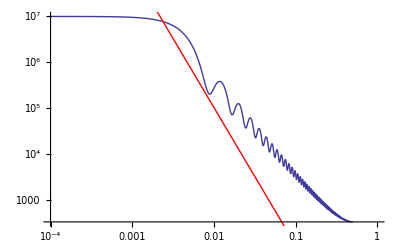

```mathematica
Show[
LogLogPlot[Simplify[exprns[128] Conjugate[exprns[128]]/.z->Exp[2Pi I f]/.Conjugate[f]->f],{f,fmin,fmax}],
LogLogPlot[10^-1 f^-3,{f,fmin,fmax},PlotStyle->{RGBColor[1,0,0]}]
]
```

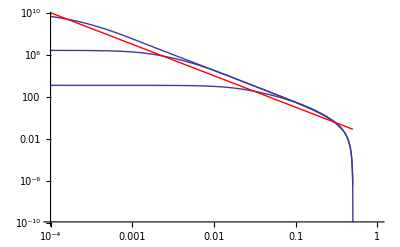

```mathematica
Show[
LogLogPlot[Simplify[exprn[32] Conjugate[exprn[32]]/.z->Exp[2Pi I f]/.Conjugate[f]->f],{f,fmin,fmax}],
LogLogPlot[Simplify[exprn[8] Conjugate[exprn[8]]/.z->Exp[2Pi I f]/.Conjugate[f]->f],{f,fmin,fmax}],
LogLogPlot[Simplify[exprn[2] Conjugate[exprn[2]]/.z->Exp[2Pi I f]/.Conjugate[f]->f],{f,fmin,fmax}],
LogLogPlot[10^-2 f^-3,{f,fmin,fmax},PlotStyle->{RGBColor[1,0,0]}]
]
```

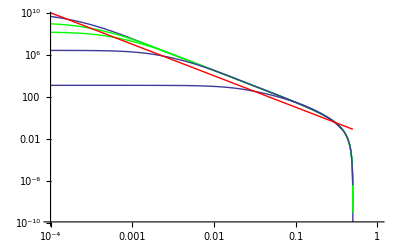

```mathematica
Show[
LogLogPlot[Simplify[exprn[32] Conjugate[exprn[32]]/.z->Exp[2Pi I f]/.Conjugate[f]->f],{f,fmin,fmax}],
LogLogPlot[Simplify[exprn[32,16] Conjugate[exprn[32,16]]/.z->Exp[2Pi I f]/.Conjugate[f]->f],{f,fmin,fmax}, PlotStyle->{RGBColor[0,1,0]}],
LogLogPlot[Simplify[exprn[32,8] Conjugate[exprn[32,8]]/.z->Exp[2Pi I f]/.Conjugate[f]->f],{f,fmin,fmax}, PlotStyle->{RGBColor[0,1,0]}],
LogLogPlot[Simplify[exprn[8] Conjugate[exprn[8]]/.z->Exp[2Pi I f]/.Conjugate[f]->f],{f,fmin,fmax}],
LogLogPlot[Simplify[exprn[2] Conjugate[exprn[2]]/.z->Exp[2Pi I f]/.Conjugate[f]->f],{f,fmin,fmax}],
LogLogPlot[10^-2 f^-3,{f,fmin,fmax},PlotStyle->{RGBColor[1,0,0]}]
]
```

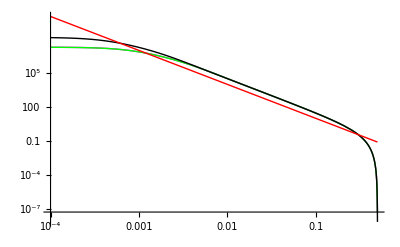

```mathematica
Show[
LogLogPlot[Simplify[exprn[8,16] Conjugate[exprn[8,16]]/.z->Exp[2Pi I f]/.Conjugate[f]->f],{f,fmin,fmax},PlotStyle->{RGBColor[2,0,1]}],
LogLogPlot[Simplify[exprn[16,8] Conjugate[exprn[16,8]]/.z->Exp[2Pi I f]/.Conjugate[f]->f],{f,fmin,fmax},PlotStyle->{RGBColor[0,1,0]}],
LogLogPlot[Simplify[exprn[16] Conjugate[exprn[16]]/.z->Exp[2Pi I f]/.Conjugate[f]->f],{f,fmin,fmax},PlotStyle->{RGBColor[0,0,0]}],
LogLogPlot[10^-2 f^-3,{f,fmin,fmax},PlotStyle->{RGBColor[1,0,0]}],PlotRange->All
]
```

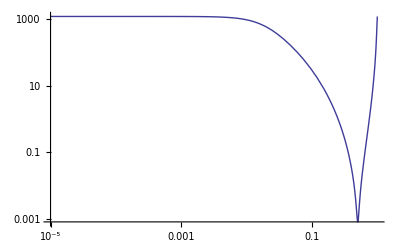

```mathematica
LogLogPlot[Simplify[(12+18 z+5 z^2)/(12-18 z+5 z^2)Conjugate[(12+18 z+5 z^2)/(12-18 z+5 z^2)]/.z->Exp[2Pi I f]/.Conjugate[f]->f],{f,10^-5,1}]
```

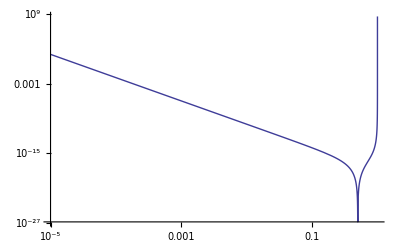

```mathematica
LogLogPlot[Simplify[10^-16(1+2z+z^2)/(1-2z+z^2)Conjugate[(1+2z+z^2)/(1-2z+z^2)]/.z->Exp[2Pi I f]/.Conjugate[f]->f],{f,10^-5,1}]
```